# Distances to Cosmological Parameters

This notebook explores using Fisher matrices to constrain cosmological parameters. For simplicity, we will only consider three cosmological parameters here : Ω_m,Ω_Λ and H_0. Please see the relevant note for a more detailed discussion of how we set up the problem.

## Setup

```mathematica
ClearAll[eHubble,mu,ngrad1,fisher1,fisher,plotContour];
```

```mathematica
eHubble[z_?NumericQ,Ωm_?NumericQ,ΩΛ_?NumericQ]:=√(Ωm (1+z)^3+ ΩΛ + (1-Ωm-ΩΛ)(1+z)^2);
```

```mathematica
(* data *)
mu[z_?NumericQ,{Ωm_?NumericQ,ΩΛ_?NumericQ,lnh_?NumericQ}]:= Log[NIntegrate[1/eHubble[z1,Ωm,ΩΛ],{z1,0,z}]]-lnh;
```

```mathematica
ngrad1[z_,ii_,x0_,h_:10^-4]:=Module[{pp,mm,tmp},
tmp=x0;
tmp[[ii]]=x0[[ii]]+h;
pp=mu[z,tmp];
tmp[[ii]]=x0[[ii]]-h;
mm=mu[z,tmp];
(pp-mm)/(2h)
];
```

```mathematica
fisher1[zlist_,icov_,p0_,ii_,jj_]:=Module[{muii,mujj},
muii=ngrad1[#,ii,p0]& /@ zlist;
mujj= ngrad1[#,jj,p0]&/@zlist;
muii.icov.mujj
];
```

```mathematica
fisher[zlist_,icov_,p0_]:=Module[{npar},
npar=Length@p0;
Table[fisher1[zlist,icov,p0,ii,jj],{ii,npar},{jj,npar}]
];
```

```mathematica
fisher[zlist_,p0_]:=fisher[zlist,10^4 IdentityMatrix@Length@zlist,p0];
```

```mathematica
plotContour[p0_,cov_,scale_:1.0]:=Module[{p1,c1,ell},
p1=p0[[1;;2]];
c1=cov[[1;;2,1;;2]]*scale;
ell=Ellipsoid[p1,c1];
Graphics[ell,PlotRange->{{0,1},{0,1}},Frame->True,
FrameLabel->{"Ωm","ΩΛ"},ImageSize->Large,LabelStyle->Large]
]
```

## Experiments

```mathematica
p0={0.3,0.7,1.0};
```

### z~0 only

```mathematica
zlist = {0.01,0.02,0.03};
fish=fisher[zlist,p0];
cov=Inverse[fish];
MatrixForm@fish
MatrixForm@cov
Sqrt[Diagonal@cov]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.904176,-1.76294,152.253},{-1.76294,3.43746,-297.559},{152.253,-297.559,30000.}} may contain significant numerical errors.

(0.904176 | -1.76294 | 152.253
-1.76294 | 3.43746 | -297.559
152.253 | -297.559 | 30000.)

(241922. | 125819. | 20.1754
125819. | 65437.9 | 10.5132
20.1754 | 10.5132 | 0.00191827)

{491.856,255.808,0.0437981}

```mathematica
{eval, evec}=Eigensystem@fish;
```

```mathematica
eval
evec//MatrixForm
```

{30003.7,0.61748,3.25353×10^-6}

(0.00507488 | -0.00991823 | 0.999938
0.461383 | -0.887131 | -0.0111409
0.887187 | 0.461411 | 0.0000740185)

### High redshift + H0

```mathematica
zlist = {800.0,900.0,1000.0};
fish=fisher[zlist,p0];
cov=Inverse[fish];
MatrixForm@fish
MatrixForm@cov
Sqrt[Diagonal@cov]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{35632.3,-8220.41,32695.1},{-8220.41,1896.47,-7542.81},{32695.1,-7542.81,30000.}} may contain significant numerical errors.

(35632.3 | -8220.41 | 32695.1
-8220.41 | 1896.47 | -7542.81
32695.1 | -7542.81 | 30000.)

(1.76859×10^9 | -4.07473×10^9 | -2.95197×10^9
-4.07473×10^9 | 9.38792×10^9 | 6.80116×10^9
-2.95197×10^9 | 6.80116×10^9 | 4.92716×10^9)

{42054.7,96891.3,70193.7}

```mathematica
{eval, evec}=Eigensystem@fish;
```

```mathematica
eval
evec//MatrixForm
```

{67528.7,0.0230493,4.98828×10^-11}

(0.726403 | -0.167582 | 0.666525
0.601978 | 0.623076 | -0.499399
-0.331605 | 0.763998 | 0.553485)

### Low redshift

(270.034 | -373.749 | 2214.3
-373.749 | 520.125 | -3158.87
2214.3 | -3158.87 | 30000.)

(0.846076 | 0.63438 | 0.00434868
0.63438 | 0.480985 | 0.00382215
0.00434868 | 0.00382215 | 0.000114813)

{0.919824,0.693531,0.0107151}

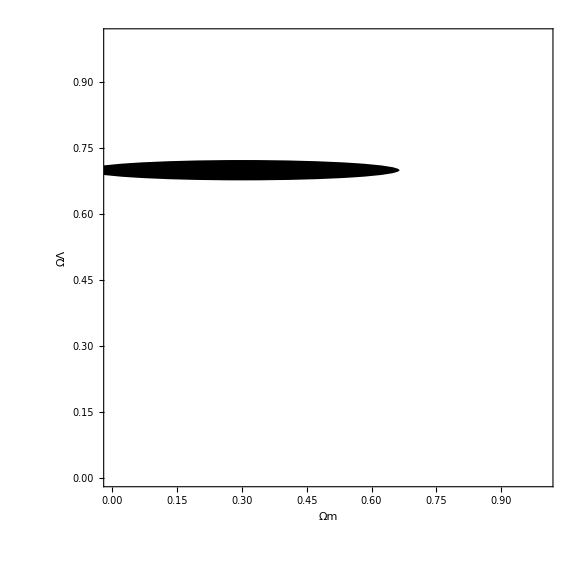

```mathematica
zlist = {0.01,0.25,0.5};
fish=fisher[zlist,p0];
cov=Inverse[fish];
MatrixForm@fish
MatrixForm@cov
Sqrt[Diagonal@cov]
plotContour[p0,cov,0.1]
```

### Design

(21701.6 | -7443.05 | 24418.4
-7443.05 | 3114.77 | -9553.47
24418.4 | -9553.47 | 30000.)

(0.00337299 | -0.0154969 | -0.00768042
-0.0154969 | 0.0849975 | 0.0396811
-0.00768042 | 0.0396811 | 0.0189212)

{0.0580775,0.291543,0.137554}

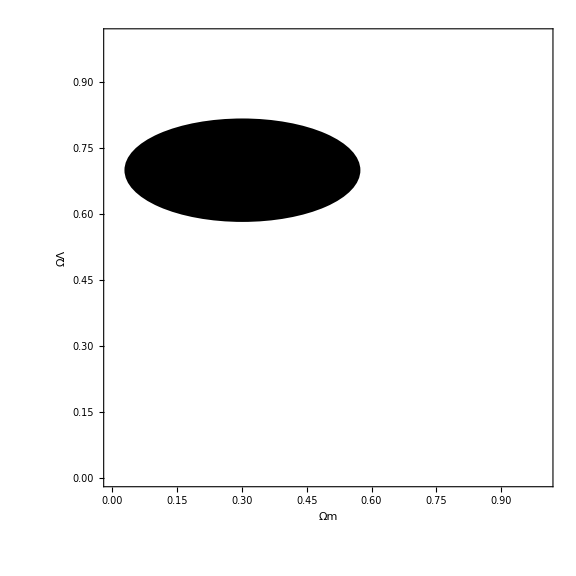

```mathematica
zlist = {2.0,10.0,1000.0};
fish=fisher[zlist,p0];
cov=Inverse[fish];
MatrixForm@fish
MatrixForm@cov
Sqrt[Diagonal@cov]
plotContour[p0,cov]
```

## Scratch